```mathematica
ex=Import["D:\\6 семестр\\Курсовая работа\\LinearTask\\LinearTask\\Data\\Answer.txt","Data"];
```

```mathematica
ListPlot3D[ex,Mesh->All,ColorFunction->"Rainbow",AxesLabel->{X,Y,U},LabelStyle->Directive[Black,Bold,FontSize->11],Axes->{True,True,True},PlotRange->All]
```

-Graphics3D-

```mathematica
Пример 1
```

```mathematica
K[x_,y_]:=x^2+y^2;
u[x_,y_]:=Sin[x y]+1;
```

```mathematica
Пример 2
```

```mathematica
u[x_,y_]:=Cos[20 x y];
K[x_,y_]:=x^2y^2;
```

```mathematica
Пример 3
```

```mathematica
u[x_,y_]:=x^2+y^2+1;
K[x_,y_]:=0.5(u[x,y])^2;
```

```mathematica
Пример 4
```

```mathematica
u[x_,y_]:=Cos[4x y]+2;
K[x_,y_]:=2+0.5(u[x,y])^2;
```

```mathematica
Пример 5
```

```mathematica
u[x_,y_]:=Cos[20x y];
K[x_,y_]:=x^2+y^2;
```

```mathematica
Пример 3
```

```mathematica
u[x_,y_]:=x^2+y^2+1;
K[x_,y_]:=( u[x,y]);
```

```mathematica
Пример 7
```

```mathematica
u[x_,y_]:=4 x^3+4 y^3+1;
K[x_,y_]:=u[x,y];
```

```mathematica
Пример 8
```

```mathematica
u[x_,y_]:=4 x^3+4 y^3+1;
K[x_,y_]:=0.5(u[x,y])^2;
```

```mathematica
ff=Solve[D[K[x,y] D[u[x,y],x],x]+D[K[x,y] D[u[x,y],y],y]==f,f][[1,1]]
```

f→-1. (16. x^2 Cos[4. x y] (2.+0.5 (2.+Cos[4. x y])^2)+16. y^2 Cos[4. x y] (2.+0.5 (2.+Cos[4. x y])^2)-16. x^2 (2.+Cos[4. x y]) Sin[4. x y]^2-16. y^2 (2.+Cos[4. x y]) Sin[4. x y]^2)

```mathematica
Simplify@%
```

f→-16. x^2 Cos[4. x y] (2.+0.5 (2.+Cos[4. x y])^2)-16. y^2 Cos[4. x y] (2.+0.5 (2.+Cos[4. x y])^2)+16. x^2 (2.+Cos[4. x y]) Sin[4. x y]^2+16. y^2 (2.+Cos[4. x y]) Sin[4. x y]^2

```mathematica
CForm[-16. x^2 Cos[4. x y] (2.+0.5 (2.+Cos[4. x y])^2)-16. y^2 Cos[4. x y] (2.+0.5 (2.+Cos[4. x y])^2)+16. x^2 (2.+Cos[4. x y]) Sin[4. x y]^2+16. y^2 (2.+Cos[4. x y]) Sin[4. x y]^2]/.{x->xx,y->yy}
```

-16.*Power(xx,2)*Cos(4.*xx*yy)*(2. + 0.5*Power(2. + Cos(4.*xx*yy),2)) - 
   16.*Power(yy,2)*Cos(4.*xx*yy)*(2. + 0.5*Power(2. + Cos(4.*xx*yy),2)) + 
   16.*Power(xx,2)*(2. + Cos(4.*xx*yy))*Power(Sin(4.*xx*yy),2) + 16.*Power(yy,2)*(2. + Cos(4.*xx*yy))*Power(Sin(4.*xx*yy),2)

```mathematica
TeXForm[-16. x^2 Cos[4. x y] (2.+0.5 (2.+Cos[4. x y])^2)-16. y^2 Cos[4. x y] (2.+0.5 (2.+Cos[4. x y])^2)+16. x^2 (2.+Cos[4. x y]) Sin[4. x y]^2+16. y^2 (2.+Cos[4. x y]) Sin[4. x y]^2]
```

-16. x^2 \cos (4. x y) \left(0.5 (\cos (4. x y)+2.)^2+2.\right)+16. x^2 \sin ^2(4. x y) (\cos (4. x y)+2.)-16. y^2 \cos (4. x y) \left(0.5 (\cos (4. x y)+2.)^2+2.\right)+16. y^2 \sin ^2(4. x y) (\cos (4. x y)+2.)

```mathematica
ff/.{x->0.0344828,y->0.0344828}
```

f→0.00590432

```mathematica
u[x_,y_]:=Cos[20x y];
```

```mathematica
Plot3D[u[x,y],{x,0,1},{y,0,1},AxesLabel->{X,Y,U}]
```

-Graphics3D-

```mathematica
error=Import["D:\\6 семестр\\Курсовая\\LinearTask\\LinearTask\\Data\\Error.txt","Data"];
```

```mathematica
error1=Import["D:\\6 семестр\\Курсовая работа\\LinearTask\\LinearTask\\Data\\Error1.txt","Data"];
ListPointPlot3D[{error1},PlotRange->All,AxesLabel->{X,Y}]
```

-Graphics3D-

```mathematica
error10=Import["D:\\6 семестр\\Курсовая работа\\LinearTask\\LinearTask\\Data\\Error10.txt","Data"];
error20=Import["D:\\6 семестр\\Курсовая работа\\LinearTask\\LinearTask\\Data\\Error20.txt","Data"];
error30=Import["D:\\6 семестр\\Курсовая работа\\LinearTask\\LinearTask\\Data\\Error30.txt","Data"];
```

```mathematica
ListPointPlot3D[{error10,error20,error30},PlotRange->All,AxesLabel->{X,Y},PlotLegends->{"h=0.111","h=0.052","h=0.034"}]
```

```mathematica
Абсолютная ошибка
```

```mathematica
absEr=Import["D:\\6 семестр\\Курсовая работа\\LinearTask\\LinearTask\\Data\\AbsError.txt","Data"];
```

```mathematica
tabEr=Table[{absEr[[i,1]],Log[absEr[[i,2]]]},{i,1,5}];
```

```mathematica
tabEr=Table[{i,Log[absEr[[i,2]]]},{i,1,5}];
```

```mathematica
absEr
```

{{0.111111,0.000127436},{0.0714286,0.0000531068},{0.0526316,0.0000288805},{0.0416667,0.000018105},{0.0344828,0.0000124091},{0.0344828,0.0000124091},{0.0344828,0.0000124091}}

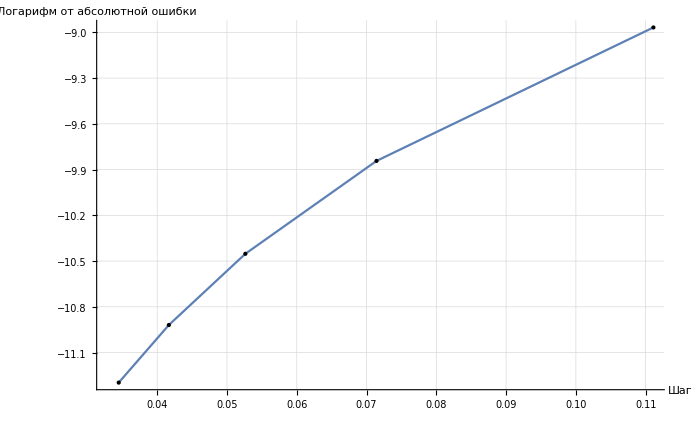

```mathematica
Show[ListLinePlot[tabEr,AxesLabel->{"Шаг","Логарифм от абсолютной ошибки"},GridLines->Automatic],Graphics[Point[tabEr]]]
```

```mathematica
Show[ListLinePlot[tabEr->{"h=0.111","h=0.071","h=0.052","h=0.041","h=0.034"},AxesLabel->{"Номер испытания","Абсолютная ошибка"}],Graphics[Point[tabEr]]]
```

-Graphics-

```mathematica
kvEr10=Import["D:\\6 семестр\\Курсовая работа\\LinearTask\\LinearTask\\Data\\kvazError10.txt","Data"];
kvEr30=Import["D:\\6 семестр\\Курсовая работа\\LinearTask\\LinearTask\\Data\\kvazError30.txt","Data"];
```

```mathematica
tabEr10=Table[{i,Log[kvEr10[[i,1]]]},{i,1,4}];
tabEr30=Table[{i,Log[kvEr30[[i,1]]]},{i,1,4}];
```

```mathematica
kvEr10[[1,1]]
```

0.0650673

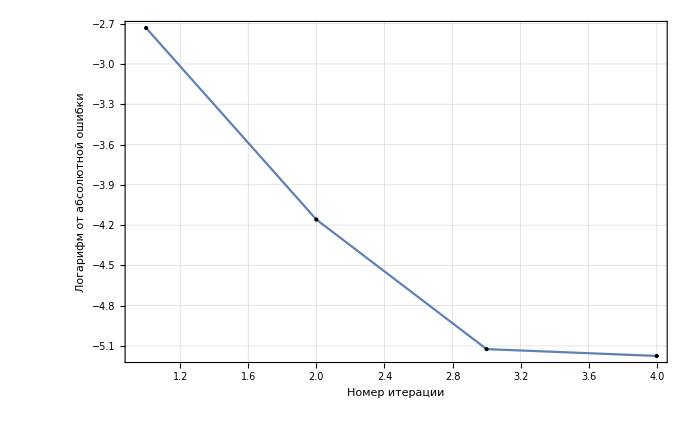

```mathematica
Show[ListLinePlot[tabEr10,AxesLabel->{"Номер итерации","Логарифм от абсолютной ошибки"},PlotTheme->"Detailed"],Graphics[Point[tabEr10]]]
```

```mathematica
tabEr10
```

{{1,0.0650673},{2,0.0156282},{3,0.00595422},{4,0.00565871}}

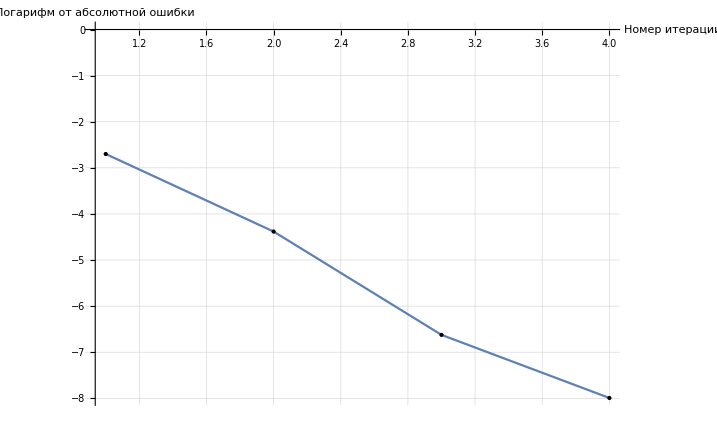

```mathematica
Show[ListLinePlot[tabEr30,AxesLabel->{"Номер итерации","Логарифм от абсолютной ошибки"},GridLines->Automatic],Graphics[Point[tabEr30]]]
```

```mathematica
tabEr30
```

{{1,0.0650673},{2,0.0156282},{3,0.00595422},{4,0.00565871}}

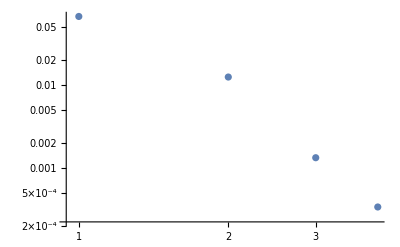

```mathematica
ListLogLogPlot[tabEr30]
```